```mathematica
TimeSeriesChart[symbols_,start_,end_,weightList_:Nothing]:=Module[{s,lists,headings,std,return,ts,tmp,values},
s=Table[FinancialData[i,{start,end}],{i,symbols}];
lists=Transpose@Normal@TimeSeriesThread[#&,s];
tmp=TimeSeries[Transpose@{First@lists,Transpose@Table[i/First@i,{i,Transpose@Last@lists}]}];
ts=TimeSeriesMap[#~Join~{If[Length@symbols>1,Mean@#,Nothing],If[TrueQ[weightList==Nothing],Nothing,Total[weightList#]]}&,tmp];
headings=symbols~Join~{"Mean","Weighted Mean"};
values=Transpose@Last@Transpose@Normal@ts;
return=Last@#&/@values;
std=StandardDeviation/@values;
TableForm@{DateListPlot[ts,PlotLegends->headings,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],
TableForm[{return,std,return/std},TableHeadings->{{"Return","SD","Return/SD"},headings}]}
]
```

{{AAPL,MSFT,AMZN,JNJ,UNH,NFLX,NVDA,INTC,ADBE,LLY},{5.46622,5.05219,4.86783,4.58808,4.06214,3.88649,3.8715,3.18083,2.90569,2.72741}}

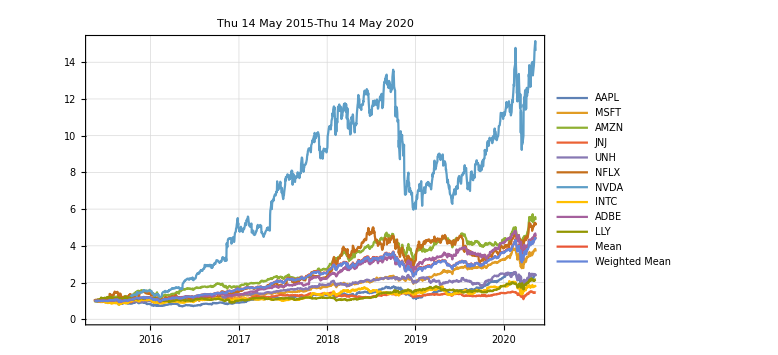
-Graphics-
 | AAPL | MSFT | AMZN | JNJ | UNH | NFLX | NVDA | INTC | ADBE | LLY | Mean | Weighted Mean
Return | 2.38581 | 3.68945 | 5.47775 | 1.44486 | 2.3454 | 5.22772 | 14.6172 | 1.75129 | 4.51416 | 2.16165 | 4.36153 | 4.33392
SD | 0.433172 | 0.768059 | 1.2536 | 0.146471 | 0.490029 | 1.30634 | 3.94798 | 0.293774 | 1.09589 | 0.286201 | 0.950236 | 0.941049
Return/SD | 5.50776 | 4.8036 | 4.3696 | 9.86446 | 4.78624 | 4.00182 | 3.70244 | 5.96136 | 4.11919 | 7.55291 | 4.58994 | 4.60541

```mathematica
{symbols,weights}=ImportString[StringDrop[Import["https://www.ishares.com/us/products/251614/ishares-msci-usa-momentum-factor-etf/1467271812596.ajax?tab=top&fileType=json","String"],3],"JSON"]//Transpose@Table[{i[[1]],i[[6,2,2]]},{i,#[[1,2]]}]&
weights=weights/Total@weights;
start=DatePlus[Today,-Quantity[5, "Years"]];
end=Today;
topChart=TimeSeriesChart[symbols,start,end,weights]
Export[FileNameJoin[{NotebookDirectory[],"topChart.svg"}],topChart];
```

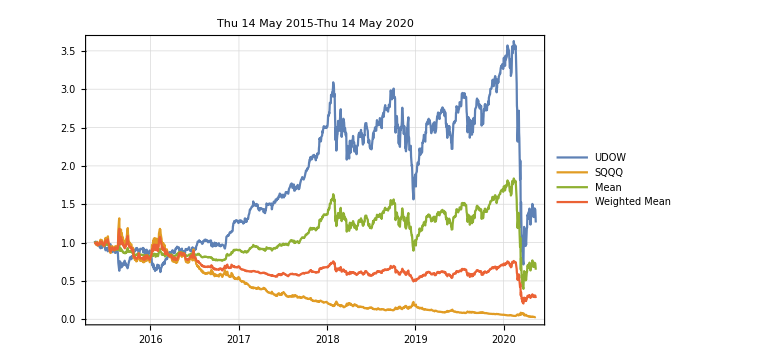
-Graphics-
 | UDOW | SQQQ | Mean | Weighted Mean
Return | 1.26139 | 0.0301523 | 0.645771 | 0.2764
SD | 0.809497 | 0.326605 | 0.277117 | 0.147363
Return/SD | 1.55824 | 0.0923205 | 2.33032 | 1.87564

```mathematica
start2=DatePlus[Today,-Quantity[5, "Years"]];
chart2=TimeSeriesChart[{"UDOW","SQQQ"},start2,end,{0.2,0.8}]
Export[FileNameJoin[{NotebookDirectory[],"chart2.svg"}],chart2];
```

```mathematica
NormalizeData[symbol_,start_,end_]:=Normal@FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
FinancialChart[symbols_,start_,end_,weightList_:Nothing]:=Module[{lists,allDates,ruleLists,listsWithMissing,mean,weighted,data,table,ts,headings},
lists=NormalizeData[#,start,end]&/@symbols;
allDates=Table[#1&@@i,{stock,lists},{i,stock}]//Fold[Union,#]&;
ruleLists=Table[#1->#2&@@i,{stock,lists},{i,stock}];
listsWithMissing=Table[Module[{association},
association=Association@a;
Table[k->association[k],{k,allDates}]],{a,ruleLists}];
mean=If[Length@symbols>1,Normal@Merge[listsWithMissing,Mean],Nothing];
weighted=If[TrueQ[weightList==Nothing],Nothing,Normal@Merge[listsWithMissing,Total[#*weightList]&]];
data=listsWithMissing~Join~{mean,weighted};
table=Table[Select[Values@d,NumberQ]//{Last@#,StandardDeviation@#}&//{#1,#2,#1/#2}&@@#&,{d,data}];
ts=Transpose@{Keys@#,Values@#}&/@data;
headings=symbols~Join~{If[Length@symbols>1,"Mean",Nothing],If[TrueQ[weightList==Nothing],Nothing,"Weighted Mean"]};
TableForm@{DateListPlot[ts,PlotLegends->headings,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],TableForm[table,TableHeadings->{headings,{"Return","Standard Deviation","Return/SD"}}]}
]
PortfolioChart[stocks_,start_,end_]:=Module[{s,mean,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
mean=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{mean};
symbols=stocks~Join~{"mean"};
std=StandardDeviation@mean[[All,2]];
return=Last@mean[[All,2]];
TableForm@{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],{return,std,return/std}//TableForm[#,TableHeadings->{{"Return","SD","Return/SD"},Automatic}]&}
]
```

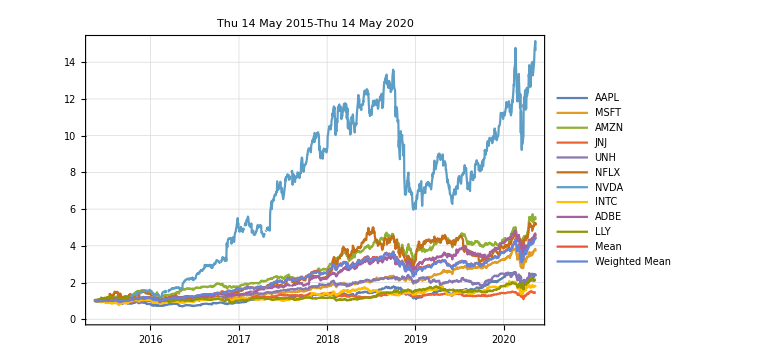
-Graphics-
 | Return | Standard Deviation | Return/SD
AAPL | 2.38581 | 0.433172 | 5.50776
MSFT | 3.68945 | 0.768059 | 4.8036
AMZN | 5.47775 | 1.2536 | 4.3696
JNJ | 1.44486 | 0.146507 | 9.86206
UNH | 2.3454 | 0.490029 | 4.78624
NFLX | 5.22772 | 1.3077 | 3.99765
NVDA | 14.6172 | 3.94697 | 3.7034
INTC | 1.75129 | 0.293774 | 5.96136
ADBE | 4.51416 | 1.09705 | 4.1148
LLY | 2.16165 | 0.286201 | 7.55291
Mean | 4.36153 | 0.950169 | 4.59026
Weighted Mean | 4.33392 | 0.940996 | 4.60567

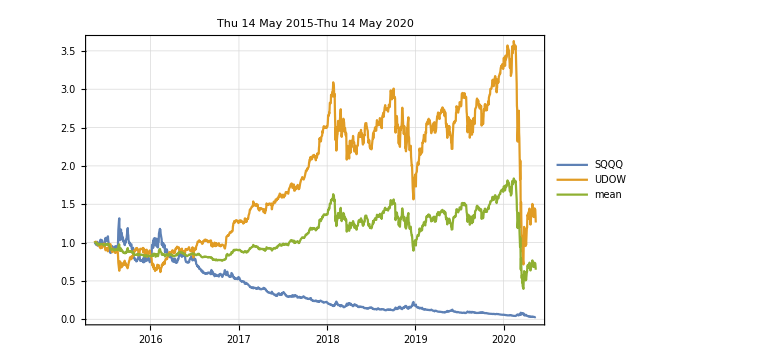
-Graphics-
Return | 0.645771
SD | 0.277117
Return/SD | 2.33032

```mathematica
FinancialChart[symbols,start,end,weights]
PortfolioChart[{"SQQQ","UDOW"},start2,end]
```